```mathematica
d=3;
l=1;

(*Import CSV filename*)
dataFileName="~/Documents/Causal/scripts/kaya_plots/csvs/pointsTime_n=15000_m=2_h=1.3.csv";


(*Extract n and m from filename*)
n=ToExpression@First@StringCases[dataFileName,"n="~~x:DigitCharacter..~~"_":>x];
m=ToExpression@First@StringCases[dataFileName,"m="~~x:DigitCharacter..~~"_":>x];

pointsTime=Import[dataFileName];


Subscript[m,c]:=Sqrt[3]/2;
M:=Sqrt[m^2+Subscript[m,c]^2];
H1=(d-1)/2+Sqrt[((d-1)/2)^2-M^2 l^2];
H2=(d-1)/2-Sqrt[((d-1)/2)^2-M^2 l^2];
norm=Gamma[H1]*Gamma[H2]/((4*π)^(d/2)*l^2*Gamma[d/2]);
W[τ_]:=norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[τ])];
Wpodal[τ_]:=norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1-Cosh[τ])];
Walpha[τ_,α_,β_]:=Cosh[2α]*W[τ]+Sinh[2α]*(Cos[β]*Re[Wpodal[τ]]-Sin[β]*Im[Wpodal[τ]]);


pdfFileName=StringJoin["~/Documents/Causal/scripts/pdfs/plot_n=",ToString[n],"_m=",ToString[m],"_Re[two_point].pdf"];

PlottingPoints=RandomSample[pointsTime,sample];
(*Export[pdfFileName,Show[ListPlot[PlottingPoints,PlotStyle->PointSize[0.00001],ImageSize->600],Plot[Re[W[τ]],{τ,0,plotLength},PlotStyle->Red,PlotRange->{{0,plotLength},{-.2,.2}}],AxesOrigin->{0,0},PlotRange->{{0,plotLength},{-.2,.2}},AxesLabel->{"Proper time τ","Re[W]"}]];*)

Print[pdfFileName];
```

RandomSample::intnm: Non-negative machine-sized integer expected at position 2 in RandomSample[<<703110216 bytes>>].

~/Documents/Causal/scripts/kaya_plots/pdfs/plot_n=15000_m=2_Re[two_point].pdf

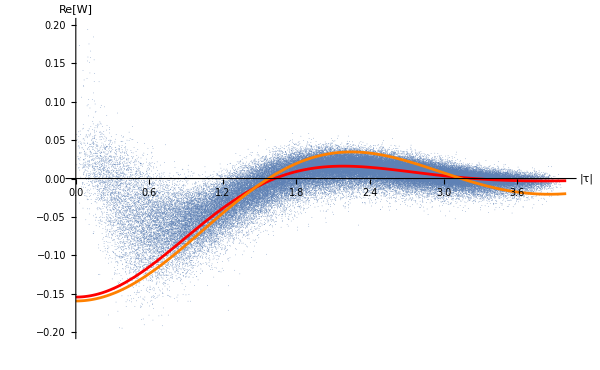

```mathematica
sample:=100000;
plotLength:=4;
f[τ_]:=E^(-I m τ)/(4 π τ)
Show[ListPlot[PlottingPoints,PlotStyle->PointSize[0.00001],ImageSize->600],Plot[Re[W[τ]],{τ,0,plotLength},PlotStyle->Red,PlotRange->{{0,plotLength},{-.2,.2}}],Plot[Im[f[τ]],{τ,0,plotLength},PlotStyle->Orange,PlotRange->{{0,plotLength},{-.2,.2}}],AxesOrigin->{0,0},PlotRange->{{0,plotLength},{-.2,.2}},AxesLabel->{Style["|τ|",16],Style["Re[W]",16]}]
```